# Cubic splines

```mathematica
ClearAll["Global`*"]
```

This file explains the basic working of cubic splines, as we use them in the online tool for generalized Pareto interpolation gpinter (wid.world/gpinter).

### Basis functions

Determine the basis functions by solving the appropriate linear system:

```mathematica
poly[x_]=Sum[Subscript[a, i] x^i,{i,0,3}]
```

a_0+x a_1+x^2 a_2+x^3 a_3

```mathematica
coef=CoefficientList[poly[x],x]
```

{a_0,a_1,a_2,a_3}

```mathematica
h00[x_]=poly[x]/.First[Solve[{poly[0]==1,poly[1]==0,poly'[0]==0,poly'[1]==0},coef]];
```

```mathematica
h01[x_]=poly[x]/.First[Solve[{poly[0]==0,poly[1]==1,poly'[0]==0,poly'[1]==0},coef]];
```

```mathematica
h10[x_]=poly[x]/.First[Solve[{poly[0]==0,poly[1]==0,poly'[0]==1,poly'[1]==0},coef]];
```

```mathematica
h11[x_]=poly[x]/.First[Solve[{poly[0]==0,poly[1]==0,poly'[0]==0,poly'[1]==1},coef]];
```

Expressions of the basis functions:

```mathematica
TableForm[Map[#&,{h00[x],h01[x],h10[x],h11[x]}],TableHeadings->{{"h00","h01","h10","h11"}}]
```

h00 | 1-3 x^2+2 x^3
h01 | 3 x^2-2 x^3
h10 | x-2 x^2+x^3
h11 | -x^2+x^3

Their first derivatives:

```mathematica
TableForm[Map[D[#,x]&,{h00[x],h01[x],h10[x],h11[x]}],TableHeadings->{{"h00","h01","h10","h11"}}]
```

h00 | -6 x+6 x^2
h01 | 6 x-6 x^2
h10 | 1-4 x+3 x^2
h11 | -2 x+3 x^2

Plots of the basis functions:

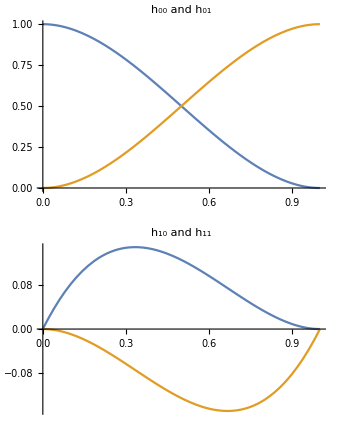

```mathematica
GraphicsColumn[{Plot[{h00[x],h01[x]},{x,0,1},PlotLabel->"h_00 and h_01"],Plot[{h10[x],h11[x]},{x,0,1},PlotLabel->"h_10 and h_11"]}]
```

Their first derivatives:

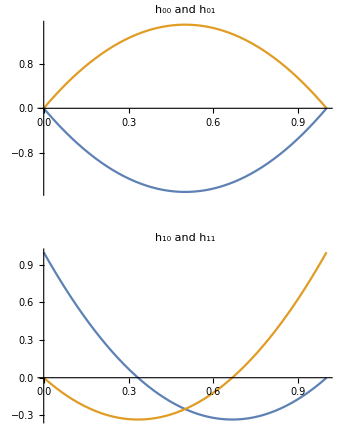

```mathematica
GraphicsColumn[{Plot[Evaluate[{h00'[x],h01'[x]}],{x,0,1},PlotLabel->"h_00 and h_01"],Plot[Evaluate[{h10'[x],h11'[x]}],{x,0,1},PlotLabel->"h_10 and h_11"]}]
```

### Interpolation function

The interpolating function over [0, 1] is a linear combination of those four basis functions:

```mathematica
h[x_,y0_,y1_,s0_,s1_]=y0*h00[x]+y1*h01[x]+s0*h10[x]+s1*h11[x];
```

```mathematica
Manipulate[GraphicsColumn[{Plot[h[x,y0,y1,s0,s1],{x,0,1},PlotRange->{{0,1},{-2,2}},PlotLabel->"Cubic spline function"],Plot[Evaluate[D[h[x,y0,y1,s0,s1],x]],{x,0,1},PlotRange->{{0,1},{-10,10}},PlotLabel->"First derivative"]}],{{y0,-1},-2,2},{{y1,1},-2,2},{{s0,0},-2,2},{{s1,0},-2,2}]
```

We can extend this function to an arbitrary interval using an affine transformation:

```mathematica
f[x_]=y0*h00[(x-x0)/(x1-x0)]+y1*h01[(x-x0)/(x1-x0)]+s0*(x1-x0)*h10[(x-x0)/(x1-x0)]+s1*(x1-x0)*h11[(x-x0)/(x1-x0)];
```

Check that the function and its derivatives have the right values:

```mathematica
{f[x0],f[x1],f'[x0],f'[x1]}
```

{y0,y1,s0,s1}

## Regularity conditions to determine the parameters of the spline

To determine the parameters of the spline, we impose the requirement that the second derivative is continuous at the jointures. That leads to the most regular curve possible in the sense that the function has the lowest curvature possible.

We start by defining two splines over the knots (x_1,x_2,x_3). The spline over (x_1,x_2) if f_1, and the one over (x_2,x_3) is f_2.

```mathematica
f1[x_]=y1*h00[(x-x1)/(x2-x1)]+y2*h01[(x-x1)/(x2-x1)]+s1*(x2-x1)*h10[(x-x1)/(x2-x1)]+s2*(x2-x1)*h11[(x-x1)/(x2-x1)];
```

```mathematica
f2[x_]=y2*h00[(x-x2)/(x3-x2)]+y3*h01[(x-x2)/(x3-x2)]+s2*(x3-x2)*h10[(x-x2)/(x3-x2)]+s3*(x3-x2)*h11[(x-x2)/(x3-x2)];
```

```mathematica
N[Solve[f1''[x2]==f2''[x2],s2]/.{x1->1,x2->5,x3->9,y1->2,y2->2,y3->5,s1->Tan[40°],s3->Tan[50°]}]
```

{{s2→0.0547867}}

Get the system in matrix form:

```mathematica
system=CoefficientArrays[{f1''[x2]==f2''[x2]},{s1,s2,s3}];
```

```mathematica
system[[1]]//Normal
```

{(6 y1)/(-x1+x2)^2-(6 y2)/(-x1+x2)^2+(6 y2)/(-x2+x3)^2-(6 y3)/(-x2+x3)^2}

```mathematica
system[[2]]//Normal
```

{{2/(-x1+x2),4/(-x1+x2)+4/(-x2+x3),2/(-x2+x3)}}

We need two additional equations for the system to be uniquely determined. At the lower end (first knot), we impose the second derivative equal to zero.

```mathematica
systemfirst=CoefficientArrays[{f1''[x1]==0},{s1,s2,s3}];
```

```mathematica
systemfirst[[1]]//Normal
```

{-(6 y1)/(-x1+x2)^2+(6 y2)/(-x1+x2)^2}

```mathematica
systemfirst[[2]]//Normal
```

{{-4/(-x1+x2),-2/(-x1+x2),0}}

At the upper end (last knot), we estimate the second derivative directly using a two-points difference:

```mathematica
systemlast=CoefficientArrays[{f2'[x3]==(y3-y2)/(x3-x2)},{s1,s2,s3}];
```

```mathematica
systemlast[[1]]//Normal
```

{-(-y2+y3)/(-x2+x3)}

```mathematica
systemlast[[2]]//Normal
```

{{0,0,1}}

Calculate explicit solution for testing purposes:

```mathematica
Simplify[Solve[{f1''[x2]==f2''[x2],f1''[x1]==0,f2'[x3]==(y3-y2)/(x3-x2)},{s1,s2,s3}]]//InputForm
```

{{s1 -> (3*x3^2*(y1 - y2) - 2*x1^2*(y2 - y3) + x2^2*(-3*y1 + y2 + 2*y3) - 
     2*x1*(3*x3*(y1 - y2) + x2*(-3*y1 + y2 + 2*y3)))/((x1 - x2)*(4*x1 - x2 - 3*x3)*(x2 - x3)), 
  s2 -> (3*x3^2*(y1 - y2) + x2^2*(3*y1 + y2 - 4*y3) + 4*x1^2*(y2 - y3) + 
     x2*(-6*x3*y1 - 8*x1*y2 + 6*x3*y2 + 8*x1*y3))/((x1 - x2)*(4*x1 - x2 - 3*x3)*(x2 - x3)), 
  s3 -> (y2 - y3)/(x2 - x3)}}